# Ondas electromagnéticas

Autora: Victoria Gómez Bifante

### Estudio en profundidad de las ondas e.m dependientes del tiempo para las primeras cuatro funciones de onda. Para la cuarta y la quinta función, deberás estudiar también su envolvente. En el penúltimo apartado B2 = 0, mientras que en el último, B2 ≠ 0. ¿Se pueden apreciar estas diferencias?

```mathematica
ClearAll["Global`*"]
```

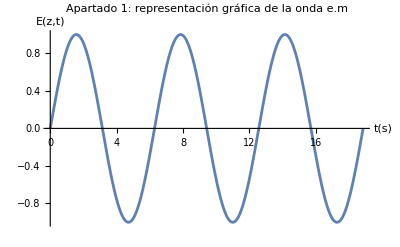

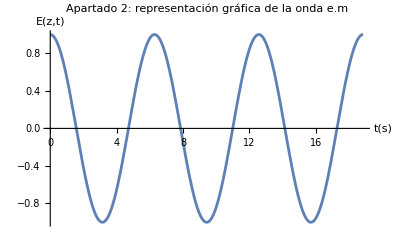

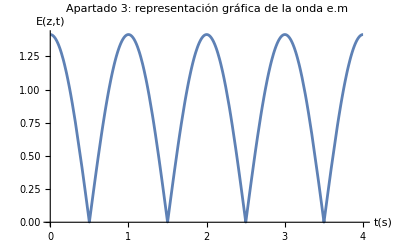

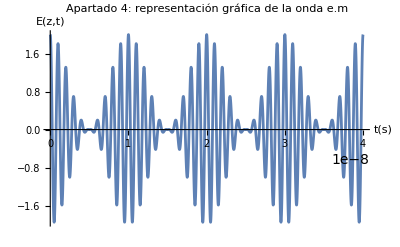

```mathematica
Plot[Sin[x],{x,0,6 Pi}, PlotLabel-> "Apartado 1: representación gráfica de la onda e.m", AxesLabel->{" t(s)","E(z,t)"}]
Plot[Cos[x],{x,0,6 Pi}, PlotLabel-> "Apartado 2: representación gráfica de la onda e.m", AxesLabel->{" t(s)","E(z,t)"}]
Plot[(1+ Cos[2*Pi*1*10^(8)*t])^(1/2),{t,0,4*10^(-8)}, PlotLabel-> "Apartado 3: representación gráfica de la onda e.m", AxesLabel->{" t(s)","E(z,t)"}]
Plot[(1+Cos[2*Pi*1*10^8*t])*Cos[2*Pi*1*10^9*t],{t,0,4*10^(-8)}, PlotLabel-> "Apartado 4: representación gráfica de la onda e.m", AxesLabel->{" t(s)","E(z,t)"}]
```

```mathematica
f[t_] :=  1 + Cos[2*Pi*1*10^(8)*t];
g[t_] := (1+Cos[2*Pi*1*10^8*t])*Cos[2*Pi*1*10^9*t]
```

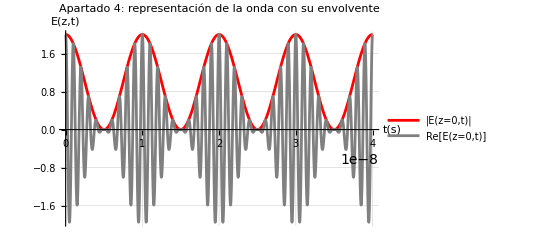

```mathematica
Plot[{1+ Cos[2*Pi*1*10^(8)*t], (1+Cos[2*Pi*1*10^8*t])*Cos[2*Pi*1*10^9*t]}, {t,0,4*10^(-8)}, PlotLegends->{"|E(z=0,t)|","Re[E(z=0,t)]"}, PlotStyle->{Red,Gray}, PlotLabel-> "Apartado 4: representación de la onda con su envolvente", AxesLabel->{" t(s)","E(z,t)"}, PlotTheme->"Grid"]
```

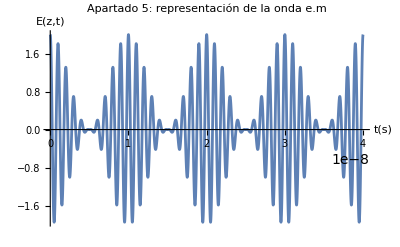

```mathematica
Plot[{Cos[2*Pi*1*10^(9)*t.b4 - 0.5*10^(-8)*200]+ Cos [2*Pi*1*10^(8)*t.b4]*Cos[2*Pi*1*10^(9)*t.b4 -  0.5*10^(-8)*200*200 ]},{t.b4, 0, 4*10^(-8)},PlotLabel-> "Apartado 5: representación de la onda e.m", AxesLabel->{" t(s)","E(z,t)"}]
```

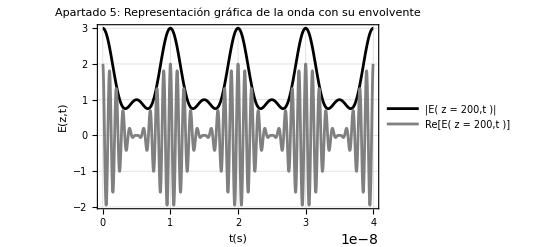

```mathematica
Plot[{1+ Cos[2*Pi*1*10^(8)*t.b4]^2 + Cos[2*Pi*1*10^(8)*t.b4],Cos[2*Pi*1*10^(9)*t.b4 - 0.5*10^(-8)*200-(1/(16*Pi))*10^(-18)*200]+ Cos [2*Pi*1*10^(8)*t.b4]*Cos[2*Pi*1*10^(9)*t.b4 - 0.5*10^(-8)*200 -(1/(16*Pi))*10^(-18)*200]},{t.b4,0,4*10^(-8)},PlotLegends->{"|E( z = 200,t )|","Re[E( z = 200,t )]"},PlotStyle->{Black ,Gray},PlotLabel->" Apartado 5: Representación gráfica de la onda con su envolvente ", AxesLabel->{" t(s)","E(z,t)"}, PlotTheme->"FullAxesGrid"]
```